```mathematica
A simple example where the rotation is relatively easy to see
```

```mathematica
P[x_,y_,z_]:=-y;
Q[x_,y_,z_]:=x;
R[x_,y_,z_]:=0;
```

```mathematica
An example with rotation in the opposite direction
```

```mathematica
P[x_,y_,z_]:=y;
Q[x_,y_,z_]:=-x;
R[x_,y_,z_]:=0;
```

```mathematica
A counterintuitive example
```

```mathematica
P[x_,y_,z_]:=x;
Q[x_,y_,z_]:=-y;
R[x_,y_,z_]:=z;
```

```mathematica
Another not so intuitive example
```

```mathematica
P[x_,y_,z_]:=-y^4;
Q[x_,y_,z_]:=0;
R[x_,y_,z_]:=0;
```

```mathematica
F[x_,y_,z_]:={P[x,y,z],Q[x,y,z],R[x,y,z]};
H[x_,y_,z_]:=Curl[F[x,y,z],{x,y,z}];
s1=VectorPlot3D[{F[x,y,z]},{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-

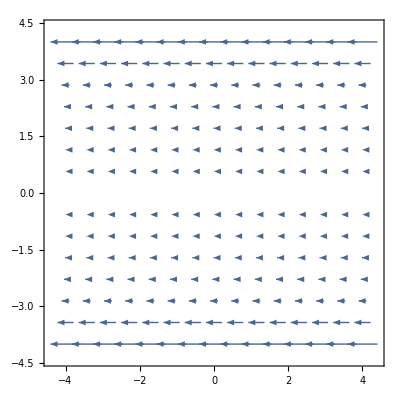

```mathematica
v=VectorPlot[{{P[x,y,0],Q[x,y,0]}},{x,-4,4},{y,-4,4}]
Show[v,m];
```

```mathematica
H[x,y,z]
s2=VectorPlot3D[{∇_{x,y,z} ×{P[x,y,z],Q[x,y,z],R[x,y,z]}},{x,-4,4},{y,-4,4},{z,-4,4},PlotTheme->"Web",VectorPoints->Coarse]
```

{0,0,4 y^3}

-Graphics3D-

```mathematica
Show[s1,s2]
```

-Graphics3D-